```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/HiggsR2GW/math

```mathematica
coord=Join[Table[Subscript[x, i][t],{i,4}],{y[t]}]
mom=D[coord, t]
n=Length[coord]
```

{x_1[t],x_2[t],x_3[t],x_4[t],y[t]}

{x_1'[t],x_2'[t],x_3'[t],x_4'[t],y'[t]}

5

```mathematica
metric=Table[If[i<=4&&j<=4,Exp[-Sqrt[2/3]coord[[5]]](KroneckerDelta[i,j]-(6 ξΓ^2 coord[[i]]coord[[j]])/(1+ξΓ Sum[coord[[k]]^2,{k,4}])),KroneckerDelta[i,j]],{i,n},{j,n}];metric//MatrixForm
```

(ⅇ^(-√(2/3) y[t]) (1-(6 ξΓ^2 x_1[t]^2)/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2))) | -(6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_1[t] x_2[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2)) | -(6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_1[t] x_3[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2)) | -(6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_1[t] x_4[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2)) | 0
-(6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_1[t] x_2[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2)) | ⅇ^(-√(2/3) y[t]) (1-(6 ξΓ^2 x_2[t]^2)/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2))) | -(6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_2[t] x_3[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2)) | -(6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_2[t] x_4[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2)) | 0
-(6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_1[t] x_3[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2)) | -(6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_2[t] x_3[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2)) | ⅇ^(-√(2/3) y[t]) (1-(6 ξΓ^2 x_3[t]^2)/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2))) | -(6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_3[t] x_4[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2)) | 0
-(6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_1[t] x_4[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2)) | -(6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_2[t] x_4[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2)) | -(6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_3[t] x_4[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2)) | ⅇ^(-√(2/3) y[t]) (1-(6 ξΓ^2 x_4[t]^2)/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2))) | 0
0 | 0 | 0 | 0 | 1)

```mathematica
inversemetric=Simplify[Inverse[metric]];inversemetric//MatrixForm
```

((ⅇ^(√(2/3) y[t]) (-1-ξΓ x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))/(-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2) | -(6 ⅇ^(√(2/3) y[t]) ξΓ^2 x_1[t] x_2[t])/(-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2) | -(6 ⅇ^(√(2/3) y[t]) ξΓ^2 x_1[t] x_3[t])/(-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2) | -(6 ⅇ^(√(2/3) y[t]) ξΓ^2 x_1[t] x_4[t])/(-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2) | 0
-(6 ⅇ^(√(2/3) y[t]) ξΓ^2 x_1[t] x_2[t])/(-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2) | (ⅇ^(√(2/3) y[t]) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2-ξΓ x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))/(-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2) | -(6 ⅇ^(√(2/3) y[t]) ξΓ^2 x_2[t] x_3[t])/(-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2) | -(6 ⅇ^(√(2/3) y[t]) ξΓ^2 x_2[t] x_4[t])/(-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2) | 0
-(6 ⅇ^(√(2/3) y[t]) ξΓ^2 x_1[t] x_3[t])/(-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2) | -(6 ⅇ^(√(2/3) y[t]) ξΓ^2 x_2[t] x_3[t])/(-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2) | (ⅇ^(√(2/3) y[t]) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))/(-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2) | -(6 ⅇ^(√(2/3) y[t]) ξΓ^2 x_3[t] x_4[t])/(-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2) | 0
-(6 ⅇ^(√(2/3) y[t]) ξΓ^2 x_1[t] x_4[t])/(-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2) | -(6 ⅇ^(√(2/3) y[t]) ξΓ^2 x_2[t] x_4[t])/(-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2) | -(6 ⅇ^(√(2/3) y[t]) ξΓ^2 x_3[t] x_4[t])/(-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2) | (ⅇ^(√(2/3) y[t]) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2))/(-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2) | 0
0 | 0 | 0 | 0 | 1)

```mathematica
viel=Transpose[Eigenvectors[inversemetric]].DiagonalMatrix[Sqrt[Eigenvalues[inversemetric]]].Inverse[Transpose[Eigenvectors[inversemetric]]]//Simplify;
```

```mathematica
viel.Transpose[viel]-inversemetric//Simplify
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 1, 1] | (6 ξΓ^2 x_1[t] (1+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2))/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[1, 2, 1] | -(6 ξΓ^3 x_1[t]^2 x_2[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[1, 2, 2] | (6 ξΓ^2 x_1[t] (1+ξΓ x_1[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2))/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[1, 3, 1] | -(6 ξΓ^3 x_1[t]^2 x_3[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[1, 3, 2] | -(6 ξΓ^3 x_1[t] x_2[t] x_3[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[1, 3, 3] | (6 ξΓ^2 x_1[t] (1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_4[t]^2))/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[1, 4, 1] | -(6 ξΓ^3 x_1[t]^2 x_4[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[1, 4, 2] | -(6 ξΓ^3 x_1[t] x_2[t] x_4[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[1, 4, 3] | -(6 ξΓ^3 x_1[t] x_3[t] x_4[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[1, 4, 4] | (6 ξΓ^2 x_1[t] (1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2))/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[1, 5, 1] | -1/(√6)
Γ[2, 1, 1] | (6 ξΓ^2 x_2[t] (1+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2))/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[2, 2, 1] | -(6 ξΓ^3 x_1[t] x_2[t]^2)/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[2, 2, 2] | (6 ξΓ^2 x_2[t] (1+ξΓ x_1[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2))/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[2, 3, 1] | -(6 ξΓ^3 x_1[t] x_2[t] x_3[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[2, 3, 2] | -(6 ξΓ^3 x_2[t]^2 x_3[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[2, 3, 3] | (6 ξΓ^2 x_2[t] (1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_4[t]^2))/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[2, 4, 1] | -(6 ξΓ^3 x_1[t] x_2[t] x_4[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[2, 4, 2] | -(6 ξΓ^3 x_2[t]^2 x_4[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[2, 4, 3] | -(6 ξΓ^3 x_2[t] x_3[t] x_4[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[2, 4, 4] | (6 ξΓ^2 x_2[t] (1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2))/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[2, 5, 2] | -1/(√6)
Γ[3, 1, 1] | (6 ξΓ^2 x_3[t] (1+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2))/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[3, 2, 1] | -(6 ξΓ^3 x_1[t] x_2[t] x_3[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[3, 2, 2] | (6 ξΓ^2 x_3[t] (1+ξΓ x_1[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2))/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[3, 3, 1] | -(6 ξΓ^3 x_1[t] x_3[t]^2)/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[3, 3, 2] | -(6 ξΓ^3 x_2[t] x_3[t]^2)/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[3, 3, 3] | (6 ξΓ^2 x_3[t] (1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_4[t]^2))/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[3, 4, 1] | -(6 ξΓ^3 x_1[t] x_3[t] x_4[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[3, 4, 2] | -(6 ξΓ^3 x_2[t] x_3[t] x_4[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[3, 4, 3] | -(6 ξΓ^3 x_3[t]^2 x_4[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[3, 4, 4] | (6 ξΓ^2 x_3[t] (1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2))/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[3, 5, 3] | -1/(√6)
Γ[4, 1, 1] | (6 ξΓ^2 x_4[t] (1+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2))/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[4, 2, 1] | -(6 ξΓ^3 x_1[t] x_2[t] x_4[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[4, 2, 2] | (6 ξΓ^2 x_4[t] (1+ξΓ x_1[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2))/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[4, 3, 1] | -(6 ξΓ^3 x_1[t] x_3[t] x_4[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[4, 3, 2] | -(6 ξΓ^3 x_2[t] x_3[t] x_4[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[4, 3, 3] | (6 ξΓ^2 x_4[t] (1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_4[t]^2))/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[4, 4, 1] | -(6 ξΓ^3 x_1[t] x_4[t]^2)/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[4, 4, 2] | -(6 ξΓ^3 x_2[t] x_4[t]^2)/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[4, 4, 3] | -(6 ξΓ^3 x_3[t] x_4[t]^2)/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[4, 4, 4] | (6 ξΓ^2 (1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2) x_4[t])/((1+ξΓ x_1[t]^2+ξΓ x_2[t]^2+ξΓ x_3[t]^2+ξΓ x_4[t]^2) (-1+ξΓ (-1+6 ξΓ) x_1[t]^2+ξΓ (-1+6 ξΓ) x_2[t]^2-ξΓ x_3[t]^2+6 ξΓ^2 x_3[t]^2-ξΓ x_4[t]^2+6 ξΓ^2 x_4[t]^2))
Γ[4, 5, 4] | -1/(√6)
Γ[5, 1, 1] | (ⅇ^(-√(2/3) y[t]) (1-(6 ξΓ^2 x_1[t]^2)/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2))))/(√6)
Γ[5, 2, 1] | -(√6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_1[t] x_2[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2))
Γ[5, 2, 2] | (ⅇ^(-√(2/3) y[t]) (1-(6 ξΓ^2 x_2[t]^2)/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2))))/(√6)
Γ[5, 3, 1] | -(√6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_1[t] x_3[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2))
Γ[5, 3, 2] | -(√6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_2[t] x_3[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2))
Γ[5, 3, 3] | (ⅇ^(-√(2/3) y[t]) (1-(6 ξΓ^2 x_3[t]^2)/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2))))/(√6)
Γ[5, 4, 1] | -(√6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_1[t] x_4[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2))
Γ[5, 4, 2] | -(√6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_2[t] x_4[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2))
Γ[5, 4, 3] | -(√6 ⅇ^(-√(2/3) y[t]) ξΓ^2 x_3[t] x_4[t])/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2))
Γ[5, 4, 4] | (ⅇ^(-√(2/3) y[t]) (1-(6 ξΓ^2 x_4[t]^2)/(1+ξΓ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2))))/(√6)

```mathematica
riemann:=riemann=Simplify[Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

```mathematica
potU=λ/4 Exp[-2Sqrt[2/3]y[t]] Sum[coord[[i]]^2,{i,4}]^2+1/(4α)(1-Exp[-Sqrt[2/3]y[t]](1+(ξg+ξΓ)Sum[coord[[i]]^2,{i,4}]))^2//Simplify
```

1/4 (ⅇ^(-2 √(2/3) y[t]) λ (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2)^2+((-1+ⅇ^(-√(2/3) y[t]) (1+(ξg+ξΓ) (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2)))^2)/α)

```mathematica
Uprime=Table[D[potU, coord[[i]]],{i,n}]//Simplify;
Upp=inversemetric.Table[D[Uprime[[j]], coord[[i]]]-Sum[affine[[k,i,j]]Uprime[[k]],{k,n}],{i,n},{j,n}]//Simplify;
```

```mathematica
Kin=1/2 mom.metric.mom//Simplify;
Hubble=Sqrt[(Kin+potU)/3]//Simplify;
eH=Kin/Hubble^2//Simplify;
```

```mathematica
Dmom=Table[D[mom[[i]], t]+Sum[affine[[i,j,k]]mom[[j]]mom[[k]],{j,n},{k,n}],{i,n}]//Simplify;
```

```mathematica
bgEoM=Table[Simplify[Dmom[[i]]+3Hubble mom[[i]]+Sum[inversemetric[[i,j]]Uprime[[j]],{j,n}]]==0,{i,n}];
```

```mathematica
bgIC={8/100(*1*)(*1/Sqrt[ξg]*),0,0,0,4(*10*)};
```

```mathematica
params={λ->10^-2,ξg->4089(*Sqrt[2 10^9 λ]/.{λ->10^-2}*),ξΓ->0,α->((3 10^4)^2)/3(*ξg^2/.{ξg->Sqrt[2 10^9 λ]/.{λ->10^-2}}*)}
Hi=Hubble/.Table[coord[[i]]->bgIC[[i]],{i,n}]/.Table[mom[[i]]->0,{i,n}]/.params;Hi//N
```

{λ→1/100,ξg→4089,ξΓ→0,α→300000000}

7.0766×10^-6

```mathematica
Plot3D[Log10[potU/.{Subscript[x, 1][t]->x,Subscript[x, 2][t]->0,Subscript[x, 3][t]->0,Subscript[x, 4][t]->0,y[t]->z}/.params],{x,-1,1},{z,-1,11}]
```

-Graphics3D-

```mathematica
tf=50 Hi^-1;
tf//N
```

7.06554×10^6

```mathematica
Dmetric=Table[(3-eH)mom[[i]]mom[[j]]+1/Hubble(Dmom[[i]]mom[[j]]+mom[[i]]Dmom[[j]]),{i,n},{j,n}].metric;
```

```mathematica
affines=Table[Subscript[Γ, i,j,k][t],{i,n},{j,n},{k,n}];
Dmoms=Table[Subscript[Dp, i][t],{i,n}];
Dms=Table[Subscript[Dm, i,j][t],{i,n},{j,n}];
Riemanns=Table[Subscript[R, i,j,k,l][t],{i,n},{j,n},{k,n},{l,n}];
Upps=Table[Subscript[U, i,j][t],{i,n},{j,n}];
```

```mathematica
bgsol=NDSolve[Join[bgEoM,Table[coord[[i]]==bgIC[[i]]/.{t->0},{i,n}],Table[mom[[i]]==0/.{t->0},{i,n}],
{NN'[t]==Hubble,NN[0]==0,Hs[t]==Hubble,eHs[t]==eH},
Flatten[Table[affines[[i,j,k]]==affine[[i,j,k]],{i,n},{j,n},{k,n}]],
Table[Dmoms[[i]]==Dmom[[i]],{i,n}],
Flatten[Table[Dms[[i,j]]==Dmetric[[i,j]],{i,n},{j,n}]],
Flatten[Table[Riemanns[[i,j,k,l]]==riemann[[i,j,k,l]],{i,n},{j,n},{k,n},{l,n}]],
Flatten[Table[Upps[[i,j]]==Upp[[i,j]],{i,n},{j,n}]]]/.params,
Join[coord,mom,Dmoms,{NN[t],Hs[t],eHs[t]},
Flatten[Table[affines[[i,j,k]],{i,n},{j,n},{k,n}]],
Table[Dmoms[[i]],{i,n}],
Flatten[Table[Dms[[i,j]],{i,n},{j,n}]],
Flatten[Table[Riemanns[[i,j,k,l]],{i,n},{j,n},{k,n},{l,n}]],
Flatten[Table[Upps[[i,j]],{i,n},{j,n}]]],
{t,0,tf}(*,WorkingPrecision->30,MaxSteps->10^6*)][[1]];//AbsoluteTiming
```

{12.0539,Null}

```mathematica
coordsol[t_]=coord/.bgsol;
momsol[t_]=mom/.bgsol;
Dmomsol[t_]=Dmoms/.bgsol;
xrsol[t_]=Sqrt[Sum[(coordsol[t][[i]])^2,{i,4}]];
x1sol[t_]=coordsol[t][[1]];
ysol[t_]=coordsol[t][[5]];
Nsol[t_]=NN[t]/.bgsol;
Hsol[t_]=Hs[t]/.bgsol;
eHsol[t_]=eHs[t]/.bgsol;
affinesol[t_]=affines/.bgsol;
Dmsol[t_]=Dms/.bgsol;
Riemannsol[t_]=Riemanns/.bgsol;
Uppsol[t_]=Upps/.bgsol;
```

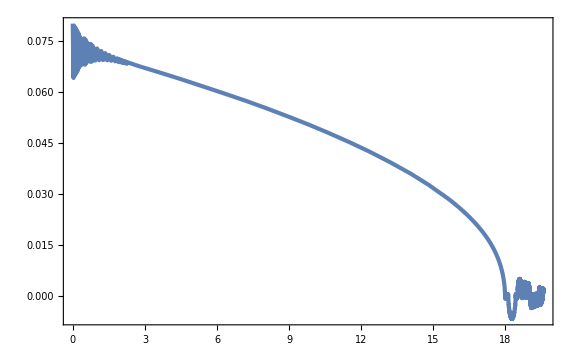

```mathematica
ParametricPlot[{Nsol[t],x1sol[t]},{t,0,tf},PlotRange->Full]
```

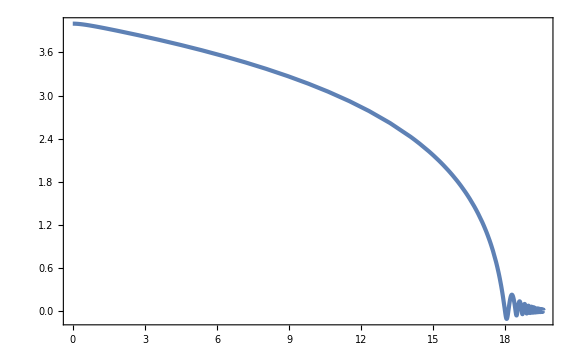

```mathematica
ParametricPlot[{Nsol[t],ysol[t]},{t,0,tf},PlotRange->Full]
```

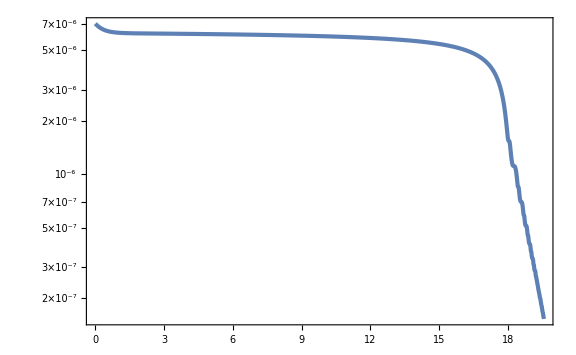

```mathematica
ParametricPlot[{Nsol[t],Hsol[t]},{t,0,tf},ScalingFunctions->{"Linear","Log"},PlotRange->Full]
```

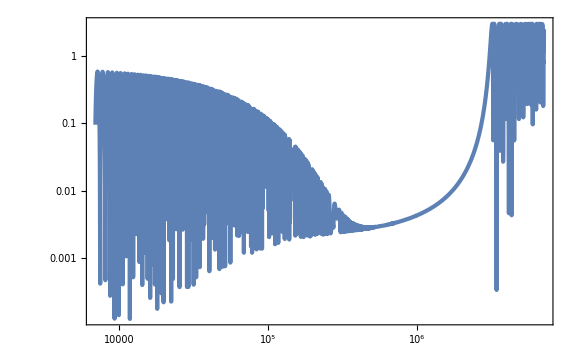

```mathematica
LogLogPlot[eHsol[t],{t,0,tf}]
```

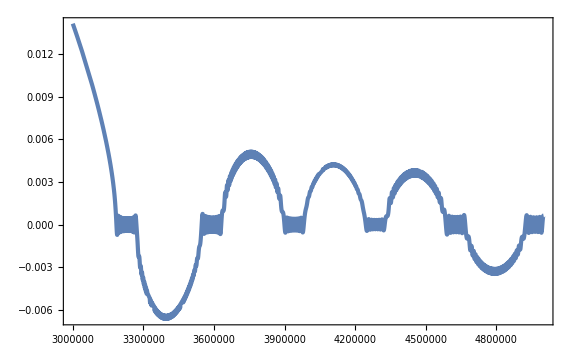

```mathematica
Plot[x1sol[t],{t,3 10^6,5 10^6},PlotRange->Full]
```

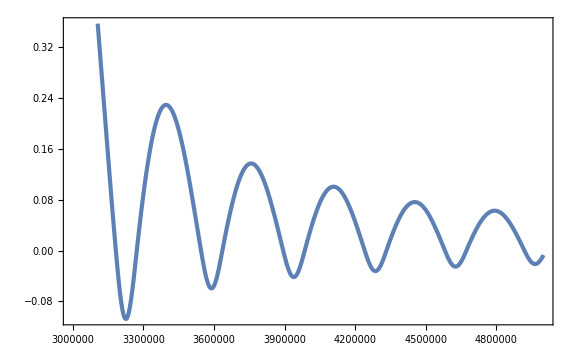

```mathematica
Plot[ysol[t],{t,3 10^6,5 10^6}]
```

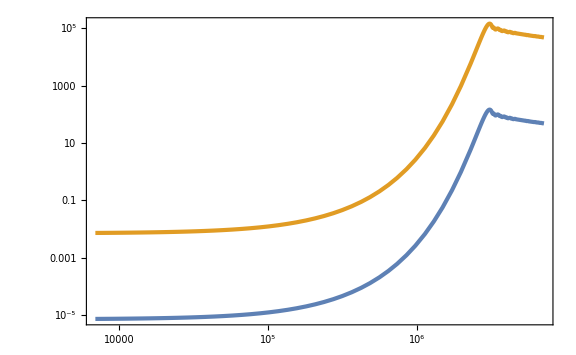

```mathematica
LogLogPlot[{E^Nsol[t] Hsol[t],1000 E^Nsol[t] Hsol[t]},{t,0,tf}]
```

```mathematica
dcoord=Table[Subscript[dx, i,a][t],{i,n},{a,n}]
dmom=D[dcoord, t];
Ddcoord=D[dcoord, t]+Table[Sum[affinesol[t][[i,j,k]]momsol[t][[j]]dcoord[[k,a]],{j,n},{k,n}],{i,n},{a,n}];//Simplify
DDdcoord=D[Ddcoord, t]+Table[Sum[affinesol[t][[i,j,k]]momsol[t][[j]]Ddcoord[[k,a]],{j,n},{k,n}],{i,n},{a,n}];//Simplify
```

{{dx_(1,1)[t],dx_(1,2)[t],dx_(1,3)[t],dx_(1,4)[t],dx_(1,5)[t]},{dx_(2,1)[t],dx_(2,2)[t],dx_(2,3)[t],dx_(2,4)[t],dx_(2,5)[t]},{dx_(3,1)[t],dx_(3,2)[t],dx_(3,3)[t],dx_(3,4)[t],dx_(3,5)[t]},{dx_(4,1)[t],dx_(4,2)[t],dx_(4,3)[t],dx_(4,4)[t],dx_(4,5)[t]},{dx_(5,1)[t],dx_(5,2)[t],dx_(5,3)[t],dx_(5,4)[t],dx_(5,5)[t]}}

```mathematica
ptbEoM=Flatten[Table[DDdcoord[[i,a]]+3Hsol[t] Ddcoord[[i,a]]-Sum[Riemannsol[t][[i,j,k,l]]momsol[t][[j]]momsol[t][[k]]dcoord[[l,a]],{j,n},{k,n},{l,n}]+qq^2/E^(2Nsol[t])dcoord[[i,a]]+Sum[Uppsol[t][[i,j]]dcoord[[j,a]],{j,n}]==(Dmsol[t].dcoord)[[i,a]],{i,n},{a,n}]];
```

```mathematica
ti=10^6;
```

```mathematica
ptbsol=NDSolve[Join[ptbEoM,Flatten[Table[dcoord[[i,a]]==1/(E^Nsol[t] Sqrt[2qq])viel[[i,a]]/.{t->ti},{i,n},{a,n}]],Flatten[Table[dmom[[i,a]]==-I/E^Nsol[t] Sqrt[qq/2]viel[[i,a]]/.{t->ti},{i,n},{a,n}]]]/.params/.{qq->10},Flatten[dcoord],{t,ti,tf}][[1]]
```

NDSolve::ntdv: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.